## Code for making PPI schematics:

Requires output from notebook that analyzes PPIs predicted by HSM and confirmed by experiment to create schematics in Fig 3 and S4.

The workhorse function here is makeInteractionLayoutBiPartite below that has a chunk of options to modify the outputs.

```mathematica
defaultEdgeWeightFunction[p_] := .01;
defaultColors = <|"Phosphosite"-> RGBColor["#007EEA"],"Proline"->RGBColor["#7FD13B"], "CTerm"-> RGBColor["#FEB80A"],"SH2"-> RGBColor["#A6D2F8"], "PTB"-> RGBColor["#59ABF1"],"Kinase_TK"-> RGBColor["#007EEA"],"PTP" -> RGBColor["#0D5BA1"],"WW"->RGBColor["#7FD13B"], "WH1"-> RGBColor["#CCEDB1"],"SH3"->RGBColor["#5E9031"], "PDZ"-> RGBColor["#FEB80A"]|>; 

Options[makeInteractionLayoutBiPartite] = {
proteinLinkThickness -> 0.15,interactionLinkThickness-> 0.1,
proteinLinkColor -> RGBColor["#DCDCDC"], interactionLinkColor -> Black,
proteinLinkStep -> 0.15, proteinLinkExtension -> 0.15,
domainWidth -> 0.1, domainHeight->0.1 ,domainRounding->0.025,
peptideWidth ->  0.05,peptideHeight-> 0.1,peptideRounding->0.025,
rescalingFactor -> .5,interProteinDistance -> .5,
typeColors -> defaultColors,labelPlot -> None
};

makeInteractionLayoutBiPartite[data_, OptionsPattern[]] := Module[
{domainLayout, protein1Graphics, protein2Graphics,proteinLinks, interactionLinks, scalingFactorProtein1, scalingFactorProtein2, colorScheme=OptionValue[typeColors],
layoutComponents, convertToShape, getProteinLink, getInteractionLink, getCurvyEnds, plabel},

scalingFactorProtein1 = If[Length[data[[1]]] < Length[data[[2]]], Max[(OptionValue[rescalingFactor] * Length[data[[2]]]) / Length[data[[1]]], 1],1] ;
scalingFactorProtein2 =  If[Length[data[[2]]] < Length[data[[1]]],Max[(OptionValue[rescalingFactor] * Length[data[[1]]]) / Length[data[[2]]], 1] ,1] ;
layoutComponents[protein_, offset_, step_, scaling_]:= MapThread[{#1-> {offset, #2}}&,{protein, Range[-(.5 * step * Length[protein] * scaling), (.5 * step * scaling * Length[protein]-.00001), step * scaling]}];

convertToShape[pmem_, {x_,y_}, scaling_] := Block[{peptides={"Proline", "Phosphosite", "CTerm"}, domains={"SH2", "SH3", "PTB", "PTP", "PDZ", "WH1", "WW", "Kinase_TK"}, peptideQ, width, height, rounding},
peptideQ = MemberQ[peptides, pmem[[1]]];
width = If[peptideQ, OptionValue[peptideWidth],OptionValue[domainWidth]] * scaling ;
height = If[peptideQ, OptionValue[peptideHeight],OptionValue[domainHeight]] * scaling;
rounding = If[peptideQ, OptionValue[peptideRounding],OptionValue[domainRounding]];
{colorScheme[pmem[[1]]], Rectangle[{x- (.5 * width), y- .5 * height}, {x+(.5 * width), y + 0.5 * height}, RoundingRadius->rounding]}
];

getProteinLink[protein_, layout_] :={Thickness[OptionValue[proteinLinkThickness]], OptionValue[proteinLinkColor], Line[Join[MinimalBy[Map[layout[#]&, protein], Last], MaximalBy[Map[layout[#]&, protein], Last]]]};
getInteractionLink[interaction_, layout_]:={Thickness[OptionValue[interactionLinkThickness]],  OptionValue[interactionLinkColor], Opacity[interaction[[-1]]], Line[{layout[interaction[[1]]], layout[interaction[[2]]]}]};

getCurvyEnds[protein_, layout_, step_, scaling_] := Block[{maxEnd, minEnd, maxX, maxY, minX, minY},
{maxX, maxY} = MaximalBy[Map[layout[#]&, protein], Last]//Flatten;
{minX, minY} = MinimalBy[Map[layout[#]&, protein], Last]//Flatten;

maxEnd = BezierCurve[{{maxX, maxY}, {maxX, maxY+step * scaling}, {maxX+0.25 * step  , maxY+step * scaling}}];
minEnd = BezierCurve[{{minX, minY}, {minX, minY-step * scaling}, {minX-0.25*step , minY-step * scaling}}];
{Thickness[OptionValue[proteinLinkThickness]],  OptionValue[proteinLinkColor], maxEnd, minEnd}
];

domainLayout = Association[Join[layoutComponents[data[[1]], 0, OptionValue[proteinLinkStep], scalingFactorProtein1], layoutComponents[data[[2]],OptionValue[interProteinDistance],OptionValue[proteinLinkStep], scalingFactorProtein2]]];
proteinLinks = {getProteinLink[data[[1]], domainLayout], getProteinLink[data[[2]], domainLayout], getCurvyEnds[data[[1]], domainLayout, OptionValue[proteinLinkExtension], scalingFactorProtein1], getCurvyEnds[data[[2]], domainLayout, OptionValue[proteinLinkExtension], scalingFactorProtein2]};
interactionLinks = Map[getInteractionLink[#, domainLayout]&, data[[3]]];

protein1Graphics = Map[convertToShape[#, domainLayout[#], scalingFactorProtein1]&, data[[1]]];
protein2Graphics = Map[convertToShape[#, domainLayout[#], scalingFactorProtein2]&, data[[2]]];
Graphics[{interactionLinks, proteinLinks,protein1Graphics, protein2Graphics}, PlotLabel-> Style[OptionValue[labelPlot], FontSize-> 8, FontFamily-> "Calibri"]]
(*If[OptionValue[labelPlot] == None, Graphics[{interactionLinks, proteinLinks,protein1Graphics, protein2Graphics}], Graphics[{interactionLinks, proteinLinks,protein1Graphics, protein2Graphics}, PlotLabel->  Style[OptionValue[labelPlot], FontSize-> 7, FontFamily-> "Calibri"]]]*)
];
```

## Fig 3: Most prevalent PPI architectures/mechanisms among those confirmed experimentally

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<< "plots/fig_3_supp_fig_4/confirmed_ppi_architectures.most_prevalent_half.txt"
```

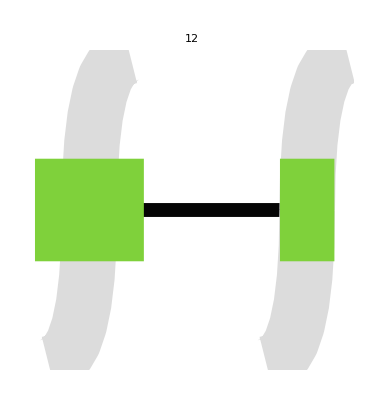
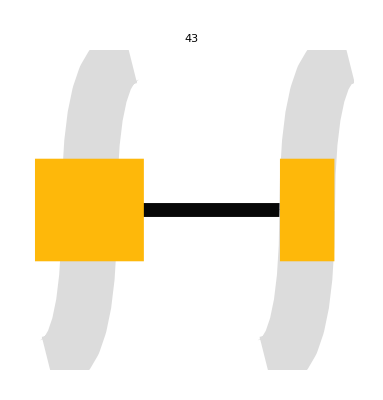
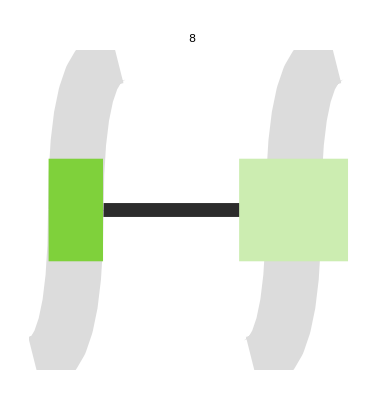
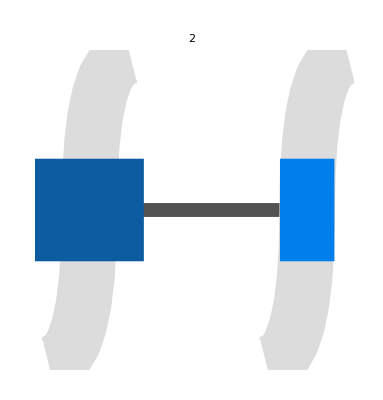
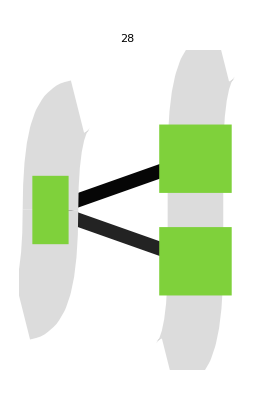
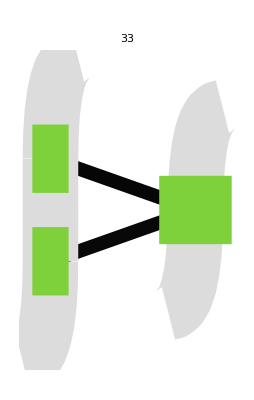
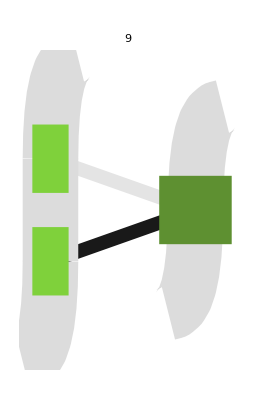
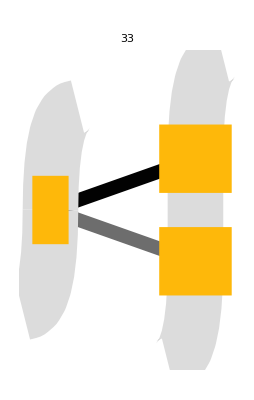

```mathematica
gtop = GraphicsGrid[Partition[Map[makeInteractionLayoutBiPartite[#, interactionLinkThickness-> .025, proteinLinkThickness-> 0.1, rescalingFactor-> 0.05, interProteinDistance-> .2, labelPlot-> #[[-1]]]&, topInteractions], UpTo[18]]]
```

```mathematica
Export["/Users/juliarogers/Desktop/current/AQLab/HSM/2022_NatMethods_correction/results/plots/fig_3_supp_fig_4/confirmed.most_prevalent_half.pdf",gtop, ImageSize-> 680, ImageResolution-> 300];
```

## Fig S4: Least prevalent PPI architectures/mechanisms among those confirmed experimentally

```mathematica
<< "plots/fig_3_supp_fig_4/confirmed_ppi_architectures.least_prevalent_half.txt"
```

```mathematica
gbot = GraphicsGrid[Partition[Map[makeInteractionLayoutBiPartite[#, interactionLinkThickness-> .025, proteinLinkThickness-> 0.1, rescalingFactor-> 0.05, interProteinDistance-> .2, labelPlot-> #[[-1]]]&, botInteractions], UpTo[15]]]
```

-Graphics-

```mathematica
Export["/Users/juliarogers/Desktop/current/AQLab/HSM/2022_NatMethods_correction/results/plots/fig_3_supp_fig_4/confirmed.least_prevalent_half.pdf",gbot, ImageSize-> 600, ImageResolution-> 300];
```

```mathematica
BarLegend[{(Blend[{White, Black}, #1]&), {0,1}}]
```